#### Aux

```mathematica
<<IGraphM`
```

IGraph/M 0.6.5 (December 21, 2022)
Evaluate IGDocumentation[] to get started.

```mathematica
ParallelNeeds["IGraphM`"]
```

```mathematica
mot2=IGShorthand[#,SelfLoops->True,VertexLabels->None,ImageSize->Tiny,VertexSize->Tiny]&/@{"1->2","2<->2<-1","1<->1->2","1<->1->2<->2","1->2->1","1<->1<->2","1<->1<->2<->2"};
```

```mathematica
mot3={-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-};
```

```mathematica
mot4=Select[Graph[#,ImageSize->36,VertexSize->0.1]&/@IGData[{"AllDirectedGraphs",4}],ConnectedGraphQ];
```

#### Human (figure 1)

```mathematica
TableForm[matPal=Uncompress@]
```

| B_cells | B_Plasma | CAFs | Cancer/epithelial | Endothelial | Mast cells | Myeloid | pericytes | T/NK
B_cells | 0 | 0 | 0 | 0 | 0.00792219 | 0 | 0.0699943 | 0 | 0
B_Plasma | 0.0125682 | 0 | 0 | 0 | 0 | 0 | 0.0172998 | 0 | 0.00452109
CAFs | 0.205773 | 0.018263 | 0.300446 | 0.121962 | 0.0582592 | 0.388938 | 0.460448 | 0.297681 | 0.2193
Cancer/epithelial | 0.127656 | 0.0240583 | 0.004611 | 0.001537 | 0.0116873 | 0.0244018 | 0.129901 | 0.001537 | 0.0466652
Endothelial | 0.0939996 | 0.0194001 | 0.0468178 | 0.0151627 | 0.0954892 | 0.0779057 | 0.175024 | 0.0597663 | 0.0459826
Mast cells | 0.0524656 | 0.00866812 | 0 | 0 | 0 | 0.0103792 | 0.0509368 | 0 | 0.0134417
Myeloid | 0.0423302 | 0.001537 | 0.0459057 | 0.0024339 | 0.0390716 | 0.044658 | 0.167511 | 0.0126696 | 0.0326386
pericytes | 0.0417965 | 0 | 0.0759256 | 0.0276912 | 0.0175044 | 0.103528 | 0.120828 | 0.0838298 | 0.0522569
T/NK | 0.0125682 | 0 | 0.00548828 | 0 | 0.015911 | 0 | 0.0188368 | 0.001537 | 0.00605809

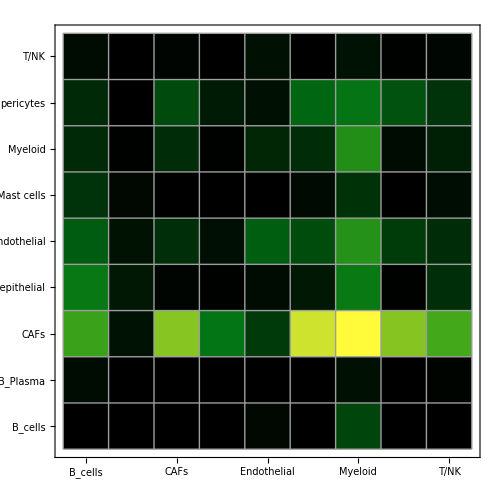
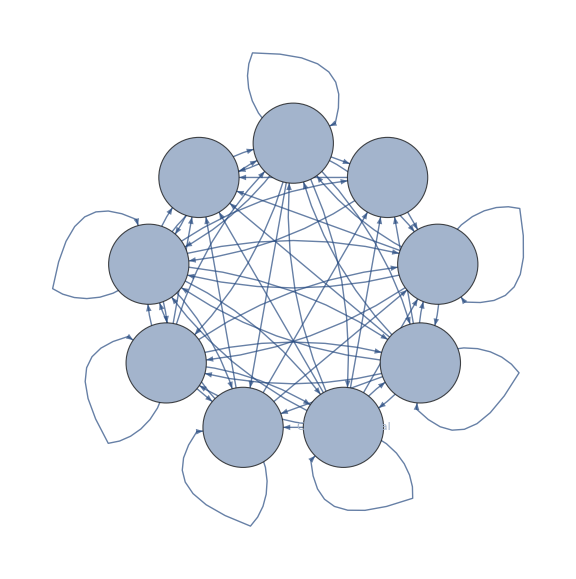

```mathematica
WmatPal=Reverse@Rest@Union@Flatten@matPal[[2;;,2;;]];
{
Row[{MatrixPlot[
Rescale@matPal[[2;;,2;;]],
Mesh->True,PlotRangePadding->None,FrameTicks->{{{Range@9,matPal[[1,2;;]]}ᵀ,None},{{Range@9,Rotate[#,π/2]&/@matPal[[1,2;;]]}ᵀ,None}},ImageSize->500,ColorFunction->"AvocadoColors",ColorFunctionScaling->False,DataReversed->True],BarLegend[{"AvocadoColors",WmatPal[[{-1,1}]]}]}],
Graph[
Rule@@matPal[[1,#+1]]/.x_String:>StringReplace[x,"_"->"\n"]&/@Position[matPal[[2;;,2;;]],_?(#>0&)],
VertexSize->.8,VertexLabels->Placed["Name",{.5,.5}],ImageSize->Large,GraphLayout->"CircularEmbedding"]}
```

```mathematica
ct=matPal[[1,2;;]];
sr=Thread[ct->{"B","B_Plasma","CAFs","Cancer\nEp","En","Mast\ncells","Myeloid","P","T/NK"}];
```

```mathematica
indexPal=(Length@ReverseSort[DeleteCases[Flatten[matPal⟦2;;,2;;⟧],0]])/2;
TH=ReverseSort[DeleteCases[Flatten[matPal⟦2;;,2;;⟧],0]][[indexPal]];
```

```mathematica
m=AdjacencyGraph[ct/.sr,UnitStep[matPal[[2;;,2;;]]-TH]];
ws=Dispatch[Thread[Flatten[Outer[DirectedEdge,ct,ct]]->Flatten[matPal[[2;;,2;;]]]]/.sr];
```

```mathematica
rootPal=MaximalBy[matPal[[2;;]],Total@#[[2;;]]&][[1,1]];
```

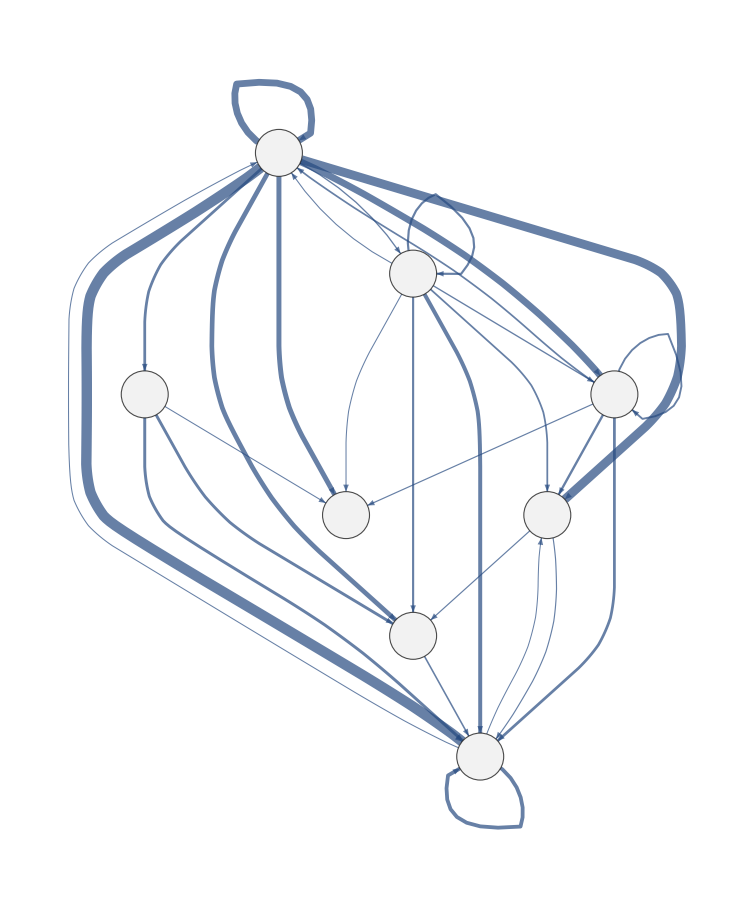

```mathematica
Graph[
#[[;;,1]],
EdgeStyle->Thread[#[[;;,1]]->(Thickness[#.01]&/@(#/(Max@#))&@#[[;;,2]])],
GraphLayout->{"LayeredDigraphEmbedding", "RootVertex"->rootPal},VertexSize->.7,VertexLabels->Placed["Name",{.5,.5}],ImageSize->750,AspectRatio->1,VertexLabels->Placed["Name",{0.5,0.5}],VertexSize->0.75,VertexStyle->GrayLevel[.95]]&@Select[Thread[Flatten[Outer[DirectedEdge,ct,ct]]->Flatten[matPal[[2;;,2;;]]]]/.sr,#[[2]]>TH&]
```

2 node motifs

```mathematica
real=Table[
Total[Mean[#/.ws]&/@(Union[Sort@EdgeList[Subgraph[m,#]]&/@(Normal/@IGLADFindSubisomorphisms[IGShorthand[c,SelfLoops->True],m,"Induced"->True])[[;;,;;,2]]])],
{c,{"1->2","2<->2<-1","1<->1->2","1<->1->2<->2","1->2->1","1<->1<->2","1<->1<->2<->2"}}];
```

```mathematica
rand=Through[{Mean,StandardDeviation}[#]]&/@(ParallelTable[
Module[{rg,ws},
rg=IGRewire[m,10000,SelfLoops->True];
ws=Dispatch[Thread[EdgeList[rg]->RandomSample[WmatPal[[;;indexPal]]]]];
Table[
Total[Mean[#/.ws]&/@(Union[Sort@EdgeList[Subgraph[rg,#]]&/@(Normal/@IGLADFindSubisomorphisms[IGShorthand[c,SelfLoops->True],rg,"Induced"->True])[[;;,;;,2]]])],
{c,{"1->2","2<->2<-1","1<->1->2","1<->1->2<->2","1->2->1","1<->1<->2","1<->1<->2<->2"}}
]
],
10^4]ᵀ);
```

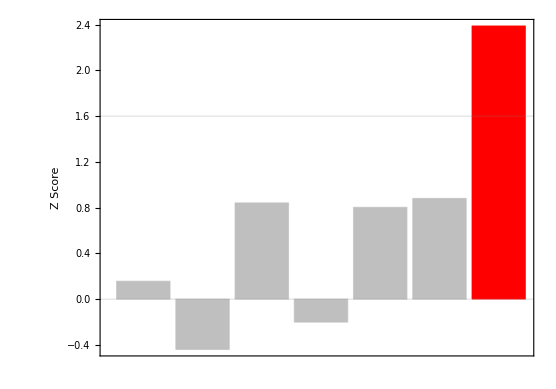

```mathematica
BarChart[Style[#,If[#>2,Red,GrayLevel[.75]]]&/@((real-rand[[;;,1]])/rand[[;;,2]]),ChartLabels->(Rotate[#,π/2]&/@mot2),PlotRange->All,Frame->True,GridLines->{None,{0,1.6}},FrameLabel->{None,"Z Score"},AspectRatio->.7,FrameTicks->{{Automatic,None},{Automatic,None}},FrameStyle->Directive[Black,14]]
```

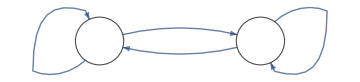
-Graphics-Interaction | Weight
CAFs->Myeloid | 0.460448
CAFs->CAFs | 0.300446
Myeloid->Myeloid | 0.167511
Myeloid->CAFs | 0.0459057
Total | 0.97431
-Graphics-Interaction | Weight
CAFs->CAFs | 0.300446
CAFs->P | 0.297681
P->P | 0.0838298
P->CAFs | 0.0759256
Total | 0.757882
-Graphics-Interaction | Weight
CAFs->CAFs | 0.300446
En->En | 0.0954892
CAFs->En | 0.0582592
En->CAFs | 0.0468178
Total | 0.501012

```mathematica
Column[
Row[Most[#1]/.{DirectedEdge[y_,z_]:>Style[(y<>"->"<>z)],x_String:>StringReplace[x,"_"->" "]},Spacer@10,Alignment->Center]&/@ReverseSortBy[
Union[(Flatten[({
Graph[
EdgeList[#1]/.x_String:>StringReplace[x,{"_"->" ","/"->"\n"}],VertexLabels->Placed["Name",{0.5,0.5}],VertexSize->0.3,VertexStyle->White,ImageSize->Medium,EdgeStyle->Thread[(EdgeList[#1]/.x_String:>StringReplace[x,{"_"->" ","/"->"\n"}])->((Thickness[#.015]&/@(#/(Max@#)))&@(EdgeList@#1/.ws))],VertexStyle->GrayLevel@.9,VertexCoordinates->{{0,0},{1,0}}],({TableForm[Join[ReverseSortBy[Transpose[{#1,#1/.ws}],Last],{Style[#,Bold]&/@{"Total",Tr[#1/.ws]}(*,{"Mean",Mean[#1/.ws]}*)}],TableHeadings->{None,{"Interaction","Weight"}}],Tr[#1/.ws]}&)[EdgeList[#1]]}&)[Subgraph[m,#1]]]&)/@(Normal/@IGLADFindSubisomorphisms[IGShorthand["1<->1<->2<->2",SelfLoops->True],m,"Induced"->True])⟦1;;All,1;;All,2⟧,SameTest->(#1⟦-1⟧==#2⟦-1⟧&)],Last]
]
```

3 node motifs

```mathematica
real3=Table[
Total[Mean[#/.ws]&/@(Union[Sort@EdgeList[Subgraph[m,#]]&/@(Normal/@IGLADFindSubisomorphisms[c,m,"Induced"->True])[[;;,;;,2]]])],
{c,Delete[mot3,{{4},{2},{1}}]}];
```

```mathematica
rand3=Through[{Mean,StandardDeviation}[#]]&/@(ParallelTable[
Module[{rg,ws},
rg=IGRewire[m,10000,SelfLoops->True];
ws=Dispatch[Thread[EdgeList[rg]->RandomSample[WmatPal[[;;indexPal]]]]];
Table[
Total[Mean[#/.ws]&/@(Union[Sort@EdgeList[Subgraph[rg,#]]&/@(Normal/@IGLADFindSubisomorphisms[c,rg,"Induced"->True])[[;;,;;,2]]])],
{c,Delete[mot3,{{4},{2},{1}}]}
]
],
10^4]ᵀ);
```

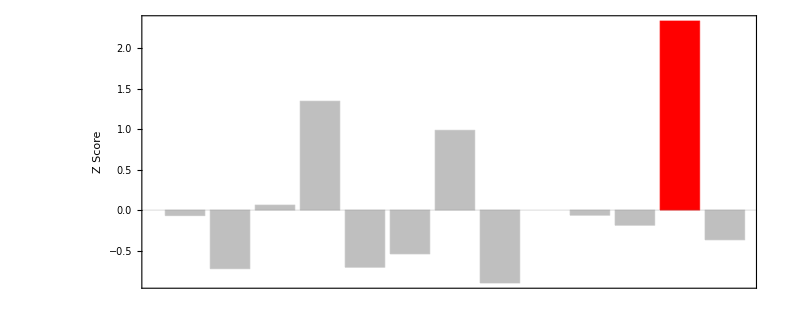

```mathematica
Quiet@BarChart[Style[#,If[#>1.8,Red,GrayLevel[.75]]]&/@((real3-rand3[[;;,1]])/rand3[[;;,2]]),ChartLabels->Delete[mot3,{{4},{2},{1}}],LabelingSize->100,PlotRange->All,Frame->True,GridLines->{None,{0}},FrameLabel->{None,"Z Score"},AspectRatio->.4,FrameTicks->{{Automatic,None},{Automatic,None}},FrameStyle->Directive[Black,14]]
```

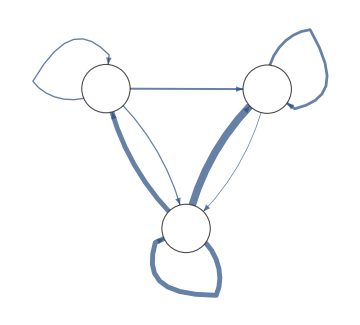
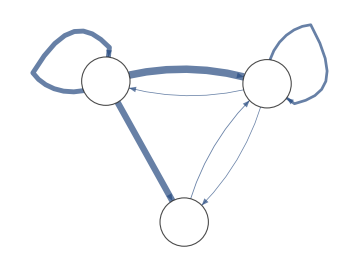
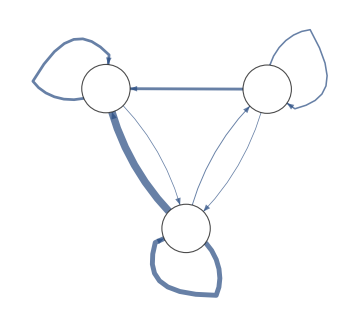
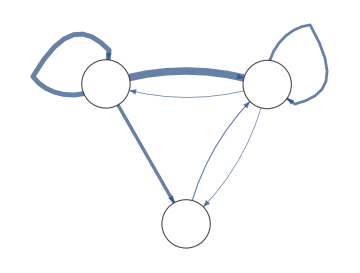
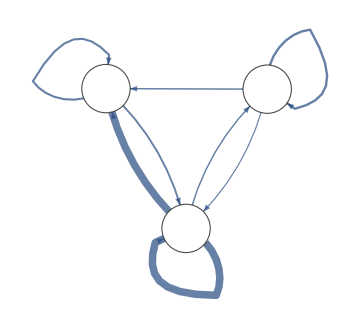
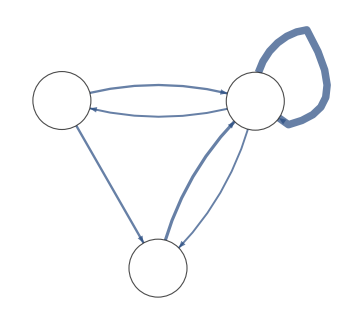
-Graphics-
Interaction | Weight
CAFs->Myeloid | 0.460448
CAFs->CAFs | 0.300446
CAFs->P | 0.297681
Myeloid->Myeloid | 0.167511
P->Myeloid | 0.120828
P->P | 0.0838298
P->CAFs | 0.0759256
Myeloid->CAFs | 0.0459057
Total | 1.55257 | -Graphics-
Interaction | Weight
CAFs->Myeloid | 0.460448
CAFs->Mast cells | 0.388938
CAFs->CAFs | 0.300446
Myeloid->Myeloid | 0.167511
Mast cells->Myeloid | 0.0509368
Myeloid->CAFs | 0.0459057
Myeloid->Mast cells | 0.044658
Total | 1.45884 | -Graphics-
Interaction | Weight
CAFs->Myeloid | 0.460448
CAFs->CAFs | 0.300446
En->Myeloid | 0.175024
Myeloid->Myeloid | 0.167511
En->En | 0.0954892
CAFs->En | 0.0582592
En->CAFs | 0.0468178
Myeloid->CAFs | 0.0459057
Total | 1.3499
-Graphics-
Interaction | Weight
CAFs->Myeloid | 0.460448
CAFs->CAFs | 0.300446
CAFs->B | 0.205773
Myeloid->Myeloid | 0.167511
B->Myeloid | 0.0699943
Myeloid->CAFs | 0.0459057
Myeloid->B | 0.0423302
Total | 1.29241 | -Graphics-
Interaction | Weight
CAFs->CAFs | 0.300446
CAFs->P | 0.297681
En->En | 0.0954892
P->P | 0.0838298
P->CAFs | 0.0759256
En->P | 0.0597663
CAFs->En | 0.0582592
En->CAFs | 0.0468178
Total | 1.01821 | -Graphics-
Interaction | Weight
Myeloid->Myeloid | 0.167511
B->Myeloid | 0.0699943
Mast cells->B | 0.0524656
Mast cells->Myeloid | 0.0509368
Myeloid->Mast cells | 0.044658
Myeloid->B | 0.0423302
Total | 0.427896

```mathematica
Grid@Partition[
Column[Most@Flatten[({
Graph[
EdgeList[#1]/.x_String:>StringReplace[x,{"_"->" ","/"->"\n"}],VertexLabels->Placed["Name",{0.5,0.5}],VertexSize->0.3,VertexStyle->White,ImageSize->Medium,EdgeStyle->Thread[(EdgeList[#1]/.x_String:>StringReplace[x,{"_"->" ","/"->"\n"}])->((Thickness[#.015]&/@(#/(Max@#)))&@(EdgeList@#1/.ws))]],({TableForm[Join[ReverseSortBy[Transpose[{#1,#1/.ws}],Last],{Style[#,Bold]&/@{"Total",Tr[#1/.ws]}}],TableHeadings->{None,{"Interaction","Weight"}}],Tr[#1/.ws]}&)[#]})],
Alignment->Center]&/@ReverseSortBy[
Union[Sort@EdgeList[Subgraph[m,#]]&/@(Normal/@IGLADFindSubisomorphisms[mot3[[15]],m,"Induced"->True])[[;;,;;,2]]],
Total[#/.ws]&
],
UpTo@3]/.x_String:>StringReplace[x,"\n"->" "]
```

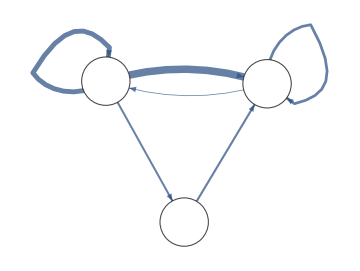
-Graphics-
Interaction | Weight
CAFs->Myeloid | 0.460448
CAFs->CAFs | 0.300446
Myeloid->Myeloid | 0.167511
Cancer Ep->Myeloid | 0.129901
CAFs->Cancer Ep | 0.121962
Myeloid->CAFs | 0.0459057
Total | 1.22617

```mathematica
Column[Most@Flatten[({
Graph[
EdgeList[#1]/.x_String:>StringReplace[x,{"_"->" ","/"->"\n"}],VertexLabels->Placed["Name",{0.5,0.5}],VertexSize->0.3,VertexStyle->White,ImageSize->Medium,EdgeStyle->Thread[(EdgeList[#1]/.x_String:>StringReplace[x,{"_"->" ","/"->"\n"}])->((Thickness[#.015]&/@(#/(Max@#)))&@(EdgeList@#1/.ws))]],({TableForm[Join[ReverseSortBy[Transpose[{#1,#1/.ws}],Last],{Style[#,Bold]&/@{"Total",Tr[#1/.ws]}}],TableHeadings->{None,{"Interaction","Weight"}}],Tr[#1/.ws]}&)[EdgeList[#1]]}&)[Subgraph[m,{"CAFs","Cancer/epithelial","Myeloid"}/.sr]]],Alignment->Center]/.x_String:>StringReplace[x,"\n"->" "]
```

4 node motifs (figure s1)

```mathematica
real4=ParallelTable[
Total[Mean[#/.ws]&/@(Union[Sort@EdgeList[Subgraph[m,#]]&/@(Normal/@IGLADFindSubisomorphisms[c,m,"Induced"->True])[[;;,;;,2]]])],
{c,mot4}];
```

```mathematica
rand4=Through[{Mean,StandardDeviation}[#]]&/@(ParallelTable[
Module[{rg,ws},
rg=IGRewire[m,10000,SelfLoops->True];
ws=Dispatch[Thread[EdgeList[rg]->RandomSample[WmatPal[[;;indexPal]]]]];
Table[
Total[Mean[#/.ws]&/@(Union[Sort@EdgeList[Subgraph[rg,#]]&/@(Normal/@IGLADFindSubisomorphisms[c,rg,"Induced"->True])[[;;,;;,2]]])],
{c,mot4}
]
],
10^4]ᵀ);
```

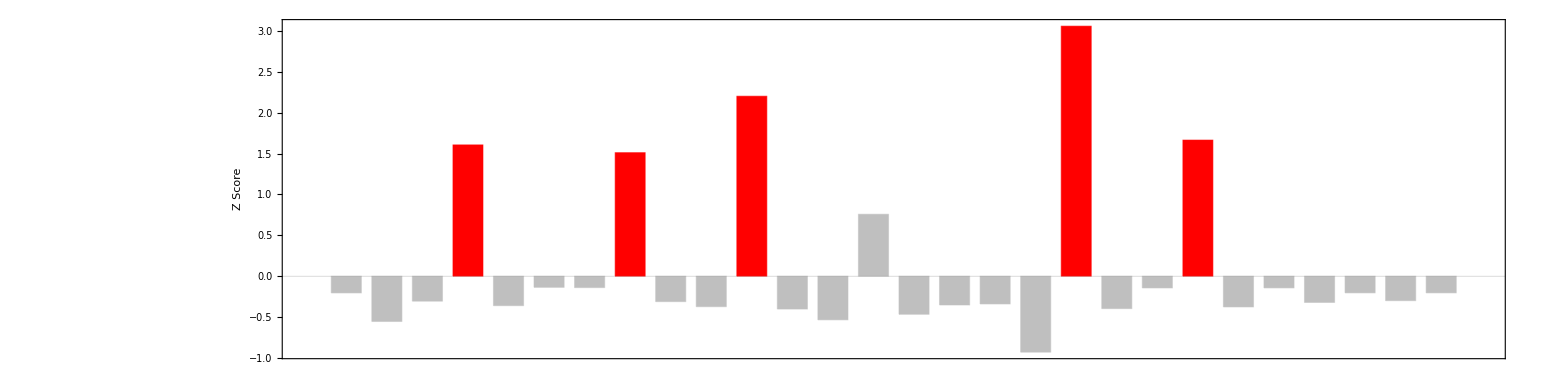

```mathematica
BarChart[Style[#,If[#>1.3,Red,GrayLevel[.75]]]&/@((#[[;;,1]]-#[[;;,2,1]])/(#[[;;,2,2]])),
ChartLabels->(Show[#,ImageSize->20]&/@#[[;;,3]]),
LabelingSize->50,PlotRange->{{0,29},All},Frame->True,GridLines->{None,{0}},FrameLabel->{None,"Z Score"},AspectRatio->.25,FrameTicks->{{Automatic,None},{Automatic,None}},FrameStyle->Directive[Black,14]]&@DeleteCases[{real4,rand4,mot4}ᵀ,{_,{_,0},_}]
```

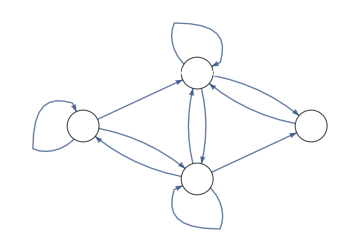
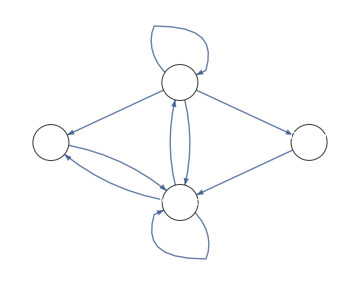
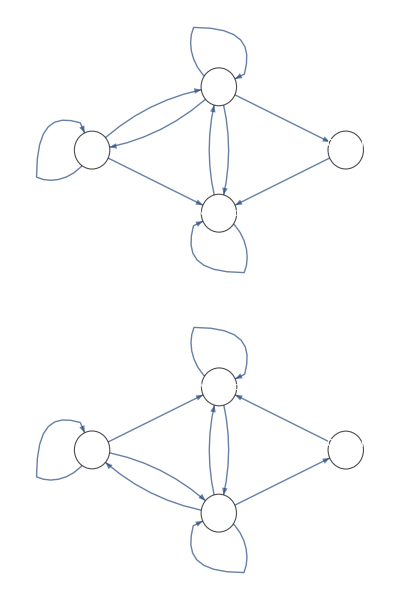
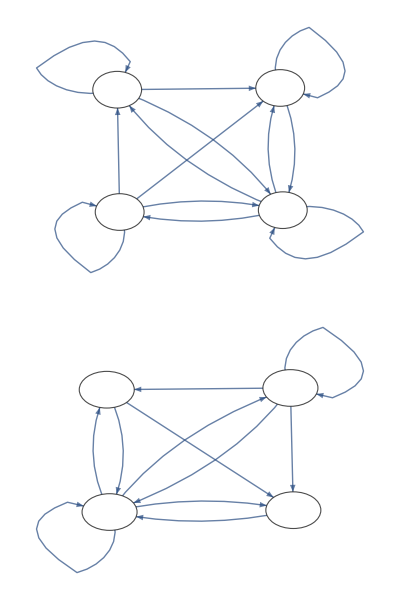
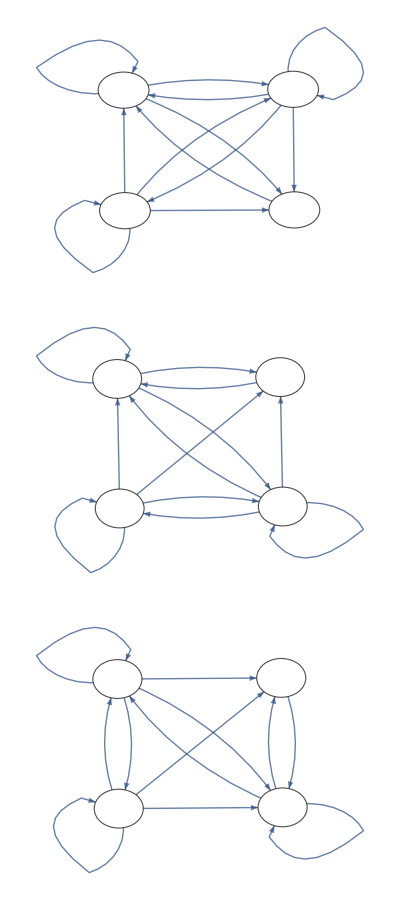
-Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics-

```mathematica
Grid[
Partition[
Table[
Column[
{Show[c[[-1]],ImageSize->Tiny],
Column[Graph[#,VertexLabels->Placed["Name",{.5,.5}],VertexSize->.3,ImageSize->Medium,VertexStyle->White,EdgeStyle->Thread[#->(#/.ws)]]&/@ReverseSortBy[Union[Sort@EdgeList[Subgraph[m,#]]&/@(Normal/@IGLADFindSubisomorphisms[c[[-1]],m,"Induced"->True])[[;;,;;,2]]],Total[#/.ws]&],Spacer@10]},
Alignment->Center],{c,Select[ReverseSortBy[DeleteCases[{real4,rand4,mot4}ᵀ,{_,{_,0},_}],(#[[1]]-#[[2,1]])/(#[[2,2]])&],
(#[[1]]-#[[2,1]])/(#[[2,2]])>1.3&]}][[{2,5,4,1,3}]],
UpTo@5],
Frame->All]
```

#### woBRCA_normal_allinteractions_withmyoe (figure s2)

```mathematica
TableForm[matwoBRCA=Uncompress@]
```

| Epithelial | Endothelial | Myoepithelial | Fibroblasts | Pericytes | T cells | Myeloid cells | B cells
Epithelial | 0.0277096 | 0.08928 | 0.0497723 | 0.032639 | 0.0175461 | 0.0162652 | 0.187434 | 0.0467255
Endothelial | 0.0509937 | 0.147286 | 0.0587629 | 0.0748406 | 0.0269548 | 0.046721 | 0.269931 | 0.068712
Myoepithelial | 0.0912924 | 0.111775 | 0.121597 | 0.0517316 | 0.0278425 | 0.0448199 | 0.210751 | 0.0591725
Fibroblasts | 0.168732 | 0.196885 | 0.213309 | 0.127391 | 0.0640877 | 0.114583 | 0.254184 | 0.0590844
Pericytes | 0.133951 | 0.137875 | 0.18855 | 0.108544 | 0.0550819 | 0.0847081 | 0.228662 | 0.0650735
T cells | 0 | 0.0469201 | 0 | 0.00438883 | 0 | 0.00378425 | 0.0715381 | 0
Myeloid cells | 0.0243992 | 0.126937 | 0.00640941 | 0.0302654 | 0.00126142 | 0.00126142 | 0.0599287 | 0.00450743
B cells | 0 | 0.00949577 | 0.00199782 | 0.00565025 | 0.00126142 | 0.00126142 | 0.0043835 | 0.00450743

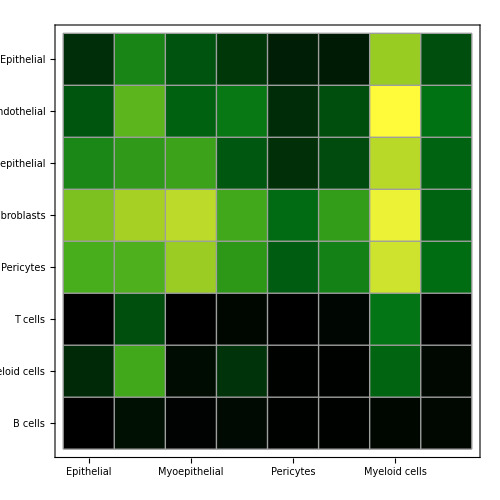
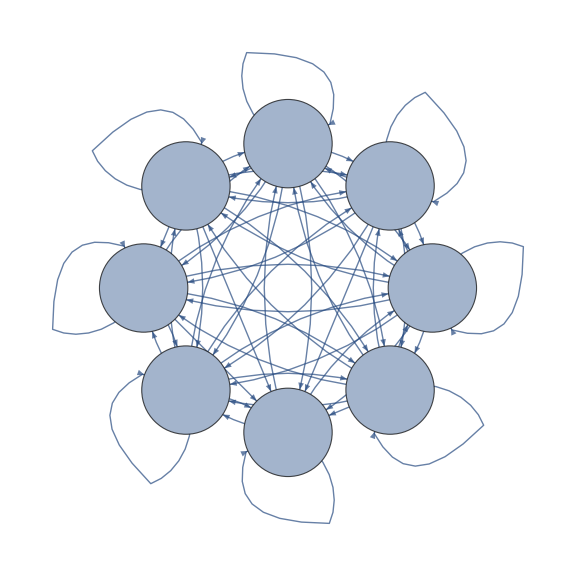

```mathematica
WmatwoBRCA=Reverse@Rest@Union@Flatten@matwoBRCA[[2;;,2;;]];
{Row[{MatrixPlot[Rescale@(matwoBRCA[[2;;,2;;]]),Mesh->True,PlotRangePadding->None,FrameTicks->{{{Range@Length@#,#}ᵀ&@matwoBRCA[[1,2;;]],None},{{Range@Length@#,Rotate[#,π/2]&/@#}ᵀ&@matwoBRCA[[1,2;;]],None}},ImageSize->500,ColorFunction->"AvocadoColors",ColorFunctionScaling->False,DataReversed->False],BarLegend[{"AvocadoColors",WmatwoBRCA[[{-1,1}]]}]}],
Graph[
Rule@@matwoBRCA[[1,#+1]]/.x_String:>StringReplace[x,"_"->"\n"]&/@Position[matwoBRCA[[2;;,2;;]],_?(#>0&)],
VertexSize->.8,VertexLabels->Placed["Name",{.5,.5}],ImageSize->Large,GraphLayout->"CircularEmbedding"]}
```

```mathematica
ctwoBRCA=matwoBRCA[[1,2;;]];
indexwoBRCA=Floor@((Length@ReverseSort[DeleteCases[Flatten[matwoBRCA⟦2;;All,2;;All⟧],0]])/2);
THwoBRCA=ReverseSort[DeleteCases[Flatten[matwoBRCA⟦2;;All,2;;All⟧],0]][[indexwoBRCA]];
mwoBRCA=AdjacencyGraph[ctwoBRCA,UnitStep[matwoBRCA[[2;;,2;;]]-THwoBRCA]];
wswoBRCA=Dispatch[Thread[Flatten@Outer[DirectedEdge,ctwoBRCA,ctwoBRCA]->Flatten[matwoBRCA[[2;;,2;;]]]]];
```

```mathematica
rootwoBRCA=MaximalBy[matwoBRCA[[2;;]],Total@#[[2;;]]&][[1,1]];
leafwoBRCA=MaximalBy[matwoBRCAᵀ[[2;;]],Total@#[[2;;]]&][[1,1]];
```

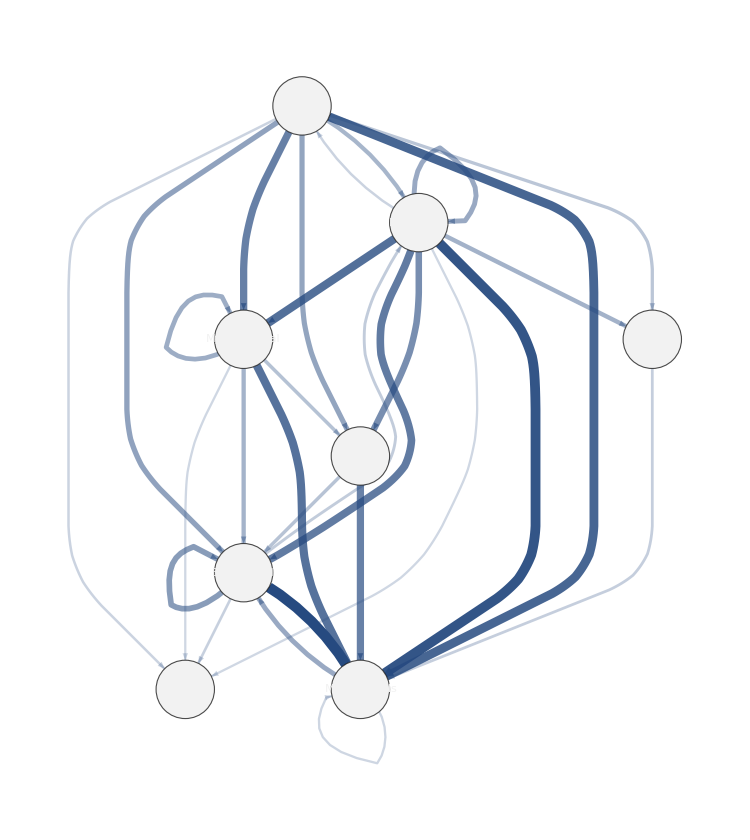

```mathematica
Module[{g,cg,mtemp=matwoBRCA/.x_Real:>If[x<THwoBRCA,0,1]},
Graph[
EdgeList[#1],
VertexLabels->Placed["Name",{0.5,0.5}],VertexSize->1,
VertexStyle->GrayLevel[.95],EdgeStyle->Thread[EdgeList[#1]->(({Thickness[#.01],Opacity[#]}&/@(#/(Max@#)))&@(EdgeList@#1/.wswoBRCA))],GraphLayout->{"LayeredDigraphEmbedding"(*,"RootVertex"->rootwoBRCA*)},VertexSize->.7,VertexLabels->Placed["Name",{.5,.5}],ImageSize->750,AspectRatio->1,EdgeWeight->EdgeList[#1]/.wswoBRCA]&@Graph[(DirectedEdge@@mtemp[[1,#]]&/@Position[mtemp,1])]
]
```

2 node motifs

```mathematica
realwoBRCA=Table[
Total[Mean[#/.wswoBRCA]&/@(Union[Sort@EdgeList[Subgraph[mwoBRCA,#]]&/@(Normal/@IGLADFindSubisomorphisms[IGShorthand[c,SelfLoops->True],mwoBRCA,"Induced"->True])[[;;,;;,2]]])],
{c,{"1->2","2<->2<-1","1<->1->2","1<->1->2<->2","1->2->1","1<->1<->2","1<->1<->2<->2"}}];
```

```mathematica
randwoBRCA=Through[{Mean,StandardDeviation}[#]]&/@(ParallelTable[
Module[{rg,ws},
rg=IGRewire[mwoBRCA,10000,SelfLoops->True];
ws=Dispatch[Thread[EdgeList[rg]->RandomSample[WmatwoBRCA[[;;indexwoBRCA]]]]];
Table[
Total[Mean[#/.ws]&/@(Union[Sort@EdgeList[Subgraph[rg,#]]&/@(Normal/@IGLADFindSubisomorphisms[IGShorthand[c,SelfLoops->True],rg,"Induced"->True])[[;;,;;,2]]])],
{c,{"1->2","2<->2<-1","1<->1->2","1<->1->2<->2","1->2->1","1<->1<->2","1<->1<->2<->2"}}
]
],
10^4]ᵀ);
```

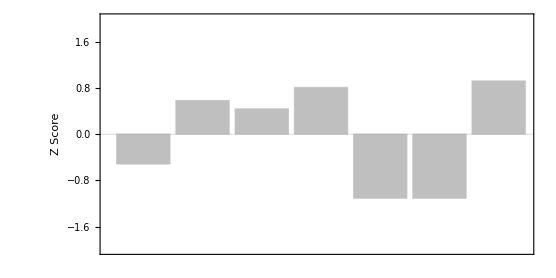

```mathematica
BarChart[Style[#,If[#>1.3,Red,GrayLevel[.75]]]&/@((realwoBRCA-randwoBRCA[[;;,1]])/randwoBRCA[[;;,2]]),ChartLabels->(Rotate[#,π/2]&/@mot2),PlotRange->{-2,2},Frame->True,GridLines->{None,{0(*,2.45*)}},FrameLabel->{None,"Z Score"},AspectRatio->.5,FrameTicks->{{Automatic,None},{Automatic,None}},FrameStyle->Directive[Black,14]]
```

```mathematica
Column[
Row[Most[#1]/.{DirectedEdge[y_,z_]:>Style[(y<>"->"<>z)],x_String:>StringReplace[x,"_"->" "]},Spacer@10,Alignment->Center]&/@ReverseSortBy[
Union[(Flatten[({
Graph[
EdgeList[#1]/.x_String:>StringReplace[x,{"_"->" ","/"->"\n"}],VertexLabels->Placed["Name",{0.5,0.5}],VertexSize->0.3,VertexStyle->White,ImageSize->Medium,EdgeStyle->Thread[(EdgeList[#1]/.x_String:>StringReplace[x,{"_"->" ","/"->"\n"}])->((Thickness[#.015]&/@(#/(Max@#)))&@(EdgeList@#1/.wswoBRCA))],VertexStyle->GrayLevel@.9,VertexCoordinates->{{0,0},{1,0}}],({TableForm[Join[ReverseSortBy[Transpose[{#1,#1/.wswoBRCA}],Last],{Style[#,Bold]&/@{"Total",Tr[#1/.wswoBRCA]}(*,{"Mean",Mean[#1/.ws]}*)}],TableHeadings->{None,{"Interaction","Weight"}}],Tr[#1/.wswoBRCA]}&)[EdgeList[#1]]}&)[Subgraph[mwoBRCA,#1]]]&)/@(Normal/@IGLADFindSubisomorphisms[IGShorthand["1<->1<->2",SelfLoops->True],mwoBRCA,"Induced"->True])⟦1;;All,1;;All,2⟧,SameTest->(#1⟦-1⟧==#2⟦-1⟧&)],Last]
]
```

3 node motifs

```mathematica
real3woBRCA=Table[
Total[Mean[#/.wswoBRCA]&/@(Union[Sort@EdgeList[Subgraph[mwoBRCA,#]]&/@(Normal/@IGLADFindSubisomorphisms[c,mwoBRCA,"Induced"->True])[[;;,;;,2]]])],
{c,Delete[mot3,{{1},{2},{4}}]}];
```

```mathematica
rand3woBRCA=Through[{Mean,StandardDeviation}[#]]&/@(ParallelTable[
Module[{rg,ws},
rg=IGRewire[mwoBRCA,10000,SelfLoops->True];
ws=Dispatch[Thread[EdgeList[rg]->RandomSample[WmatwoBRCA[[;;indexwoBRCA]]]]];
Table[
Total[Mean[#/.ws]&/@(Union[Sort@EdgeList[Subgraph[rg,#]]&/@(Normal/@IGLADFindSubisomorphisms[c,rg,"Induced"->True])[[;;,;;,2]]])],
{c,Delete[mot3,{{4},{2},{1}}]}
]
],
10^4]ᵀ);
```

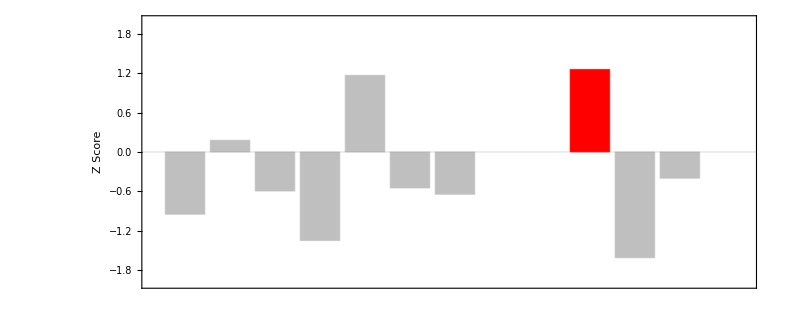

```mathematica
BarChart[Style[#,If[#>1.2,Red,GrayLevel[.75]]]&/@((real3woBRCA-rand3woBRCA[[;;,1]])/rand3woBRCA[[;;,2]]),ChartLabels->Delete[mot3,{{1},{2},{4}}],LabelingSize->100,PlotRange->{-2,2},Frame->True,GridLines->{None,{0}},FrameLabel->{None,"Z Score"},AspectRatio->.4,FrameTicks->{{Automatic,None},{Automatic,None}},FrameStyle->Directive[Black,14]]//Quiet
```

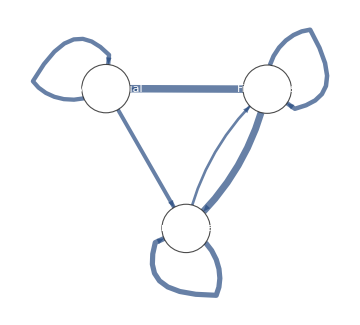
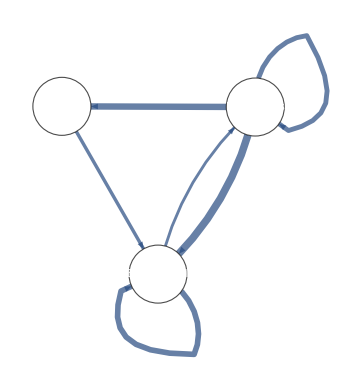
-Graphics-
Interaction | Weight
Fibroblasts->Myoepithelial | 0.213309
Fibroblasts->Endothelial | 0.196885
Endothelial->Endothelial | 0.147286
Fibroblasts->Fibroblasts | 0.127391
Myoepithelial->Myoepithelial | 0.121597
Myoepithelial->Endothelial | 0.111775
Endothelial->Fibroblasts | 0.0748406
Total | 0.993083 | -Graphics-
Interaction | Weight
Fibroblasts->Endothelial | 0.196885
Fibroblasts->Epithelial | 0.168732
Endothelial->Endothelial | 0.147286
Fibroblasts->Fibroblasts | 0.127391
Epithelial->Endothelial | 0.08928
Endothelial->Fibroblasts | 0.0748406
Total | 0.804415

```mathematica
Grid@Partition[
Column[Most@Flatten[({
Graph[
EdgeList[#1]/.x_String:>StringReplace[x,{"_"->" ","/"->"\n"}],VertexLabels->Placed["Name",{0.5,0.5}],VertexSize->0.3,VertexStyle->White,ImageSize->Medium,EdgeStyle->Thread[(EdgeList[#1]/.x_String:>StringReplace[x,{"_"->" ","/"->"\n"}])->((Thickness[#.015]&/@(#/(Max@#)))&@(EdgeList@#1/.wswoBRCA))]],({TableForm[Join[ReverseSortBy[Transpose[{#1,#1/.wswoBRCA}],Last],{Style[#,Bold]&/@{"Total",Tr[#1/.wswoBRCA]}}],TableHeadings->{None,{"Interaction","Weight"}}],Tr[#1/.wswoBRCA]}&)[#]})],
Alignment->Center]&/@ReverseSortBy[
Union[Sort@EdgeList[Subgraph[mwoBRCA,#]]&/@(Normal/@IGLADFindSubisomorphisms[mot3[[13]],mwoBRCA,"Induced"->True])[[;;,;;,2]]],
Total[#/.wswoBRCA]&
],
UpTo@3]
```

4 node motifs

```mathematica
real4woBRCA=ParallelTable[
Total[Mean[#/.wswoBRCA]&/@(Union[Sort@EdgeList[Subgraph[mwoBRCA,#]]&/@(Normal/@IGLADFindSubisomorphisms[c,mwoBRCA,"Induced"->True])[[;;,;;,2]]])],
{c,mot4}];
```

```mathematica
rand4woBRCA=Through[{Mean,StandardDeviation}[#]]&/@(ParallelTable[
Module[{rg,ws},
rg=IGRewire[mwoBRCA,10000,SelfLoops->True];
ws=Dispatch[Thread[EdgeList[rg]->RandomSample[WmatwoBRCA[[;;indexwoBRCA]]]]];
Table[
Total[Mean[#/.ws]&/@(Union[Sort@EdgeList[Subgraph[rg,#]]&/@(Normal/@IGLADFindSubisomorphisms[c,rg,"Induced"->True])[[;;,;;,2]]])],
{c,mot4}
]
],
10^4]ᵀ);
```

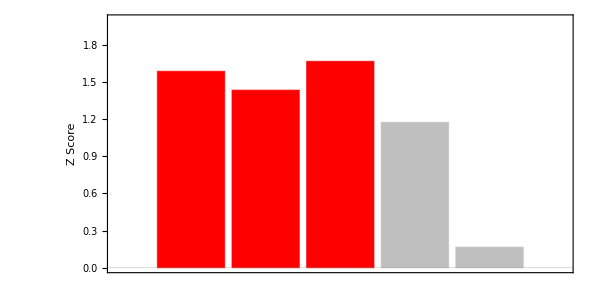

```mathematica
BarChart[Style[#,If[#>1.2,Red,GrayLevel[.75]]]&/@((#[[;;,1]]-#[[;;,2,1]])/(#[[;;,2,2]])),
ChartLabels->(Show[#,ImageSize->70]&/@#[[;;,3]]),
LabelingSize->50,PlotRange->{{0,6},{0,2}},Frame->True,GridLines->{None,{0}},FrameLabel->{None,"Z Score"},AspectRatio->.5,FrameTicks->{{Automatic,None},{Automatic,None}},FrameStyle->Directive[Black,14]]&@DeleteCases[{real4woBRCA,rand4woBRCA,mot4}ᵀ,{_,{_,0},_}]
```

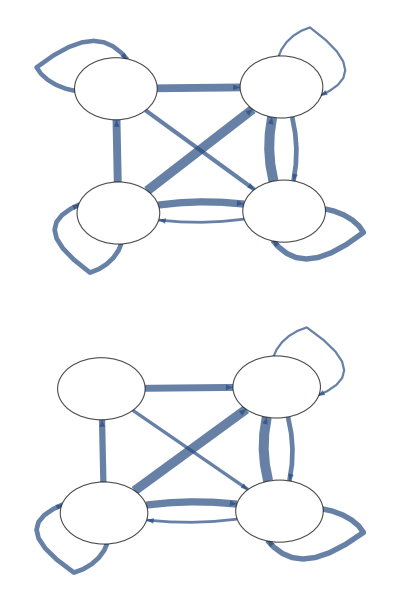
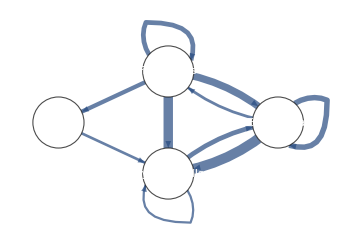
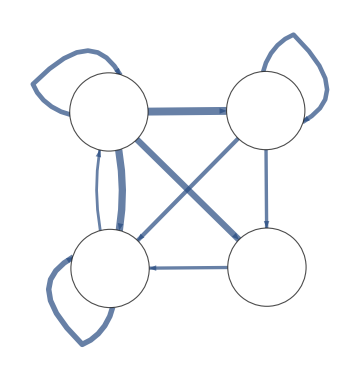
-Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics-

```mathematica
Grid[
Partition[
Table[
Column[
{Show[c[[-1]],ImageSize->Tiny],
Column[Graph[#,VertexLabels->Placed["Name",{.5,.5}],VertexSize->.5,ImageSize->Medium,VertexStyle->White,EdgeStyle->Thread[#->(#/.ws1woBRCA)]]&/@ReverseSortBy[Union[Sort@EdgeList[Subgraph[mwoBRCA,#]]&/@(Normal/@IGLADFindSubisomorphisms[c[[-1]],mwoBRCA,"Induced"->True])[[;;,;;,2]]],Total[#/.wswoBRCA]&],Spacer@10]},
Alignment->Center],{c,Select[ReverseSortBy[DeleteCases[{real4woBRCA,rand4woBRCA,mot4}ᵀ,{_,{_,0},_}],(#[[1]]-#[[2,1]])/(#[[2,2]])&],
(#[[1]]-#[[2,1]])/(#[[2,2]])>1.3&]}],
UpTo@5],
Frame->All]
```